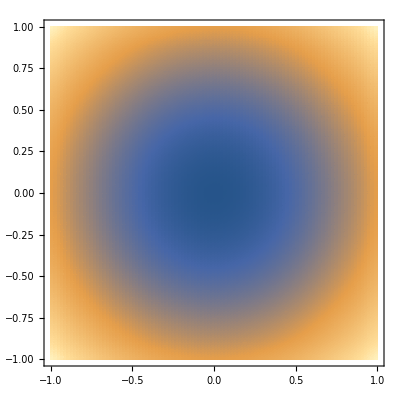

```mathematica
f1[x_,y_]:=x^2+y^2
dk=0.1;
da=Table[f1[x,y],{x,-1,1,dk},{y,-1,1,dk}];
ListDensityPlot[da,DataRange->{{-1,1},{-1,1}},InterpolationOrder->3]
```